# FIttability (141120)

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Dropbox (AG NRO)\Gonzalo\My Stuff\Master thesis\Thermal Imaging\Thermal Imaging Data\140908 Mouse 4(Power correlation)

```mathematica
samplingRate=1000./128
```

7.8125

```mathematica
gagFiles=FileNames["*.mat"]
```

{140908-01-200um-5mW,500ms,0'2Hz,40T.mat,140908-02-200um-2,5mW,500ms,0'2Hz,40T.mat,140908-03-200um-5mW,500ms,0'2Hz,40T.mat,140908-04-200um-7,5mW,500ms,0'2Hz,40T.mat,140908-05-200um-10mW,500ms,0'2Hz,40T.mat,140908-06-200um-5mW,500ms,0'2Hz,40T.mat,140908-07-200um-2,5mW,2000ms,0'2Hz,40T.mat,140908-08-200um-20mW,10ms,0'2Hz,40T(pulsed at 25Hz).mat}

## 5 mW 500 ms

## Functions

```mathematica
baselineNormalize[data_]:=Module[{},
(#-Mean[#[[1;;9]]])&/@data
];
```

```mathematica
(*meanBandPlot[data_, color_]:=Module[{means, sds},
means=Mean/@Transpose[data];
sds=StandardDeviation/@Transpose[data];
ListLinePlot[{means-sds, means+sds},
PlotStyle->None,
PlotRange->All,
Filling->{1->{{2},Opacity[1,color]}}
]
];*)
```

```mathematica
meanBandPlot[data_, color_, dataRange_:Automatic,legend_]:=
Module[{means,timePoints,sds},
means=Mean/@Transpose[data];
sds=StandardDeviation/@Transpose[data];
If[dataRange===Automatic,
ListLinePlot[{means-sds, means+sds},PlotStyle->None,
PlotRange->All,
Filling->{1->{{2},Opacity[1,color]}},
PlotLegends->gagLegend],
timePoints=Rescale[Range[Length[means]],{1,Length[means]},dataRange];
ListLinePlot[{Transpose[{timePoints,means-sds}],Transpose[{timePoints,means+sds}]},PlotStyle->None,
PlotRange->All,
Filling->{1->{{2},Opacity[1,color]}},
PlotLegends->legend]
]
];
```

```mathematica
meanPlot[data_, color_, dataRange_:Automatic]:=
Module[{means,timePoints},
means=Mean/@Transpose[data];
If[dataRange===Automatic,
ListLinePlot[means,PlotStyle->{color,Thick}],
timePoints=Rescale[Range[Length[means]],{1,Length[means]},dataRange];
ListLinePlot[Transpose[{timePoints,means}],
PlotStyle->{color,Thick},PlotRange->All]
]


];
```

```mathematica
SDPlot[data_, color_, dataRange_:Automatic]:=
Module[{sds,timePoints},
sds=StandardDeviation/@Transpose[data];
If[dataRange===Automatic,
ListLinePlot[sds,PlotStyle->{color,Thick}],
timePoints=Rescale[Range[Length[sds]],{1,Length[sds]},dataRange];
ListLinePlot[Transpose[{timePoints,sds}],
PlotStyle->{color,Thick},PlotRange->All]
]
];
```

```mathematica
means[data_]:=Module[{means, sds},
Mean/@Transpose[data]
];
```

```mathematica
trialPointPlot[data_, color_]:=Module[{},
ListPlot[data,PlotStyle->Opacity[0.2,color]]
];
```

```mathematica
trialPointLogPlot[data_, color_]:=Module[{},
ListLogPlot[data,PlotStyle->Opacity[0.2,color]]
];
```

```mathematica
gagColors= {LightBlue,Blue,Darker[Blue],Purple,Pink,Red,Orange,Yellow,LightGreen,Green, Darker[Green]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
gagColors=Table[ColorData["GrayTones",1-n],{n,0.2,1,0.8/3}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Load Data

```mathematica
gagFitDataFittability=Map[Import,gagFiles];
Dimensions[gagFitDataFittability]
```

{8,1}

```mathematica
Dimensions[Transpose[gagFitDataFittability]]
```

{1,8}

```mathematica
gagFitDataFittability=Flatten[gagFitDataFittability,1];
Dimensions[gagFitDataFittability]
```

{8}

```mathematica
Dimensions[gagFitDataFittability[[3]]]
```

{40,620}

```mathematica
gagFitDataFittability= gagFitDataFittability[[7]];
Dimensions[gagFitDataFittability]
```

{40,620}

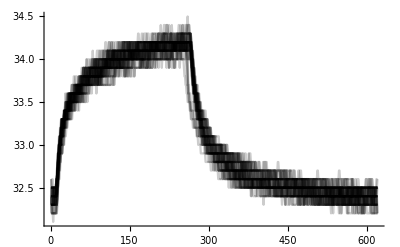

```mathematica
gagTemp=ListLinePlot[gagFitDataFittability,PlotStyle->Opacity[0.2,Black],PlotRange->All]
```

```mathematica
Ordering[gagFitDataFittability[[;;, 1]],1]
```

{1}

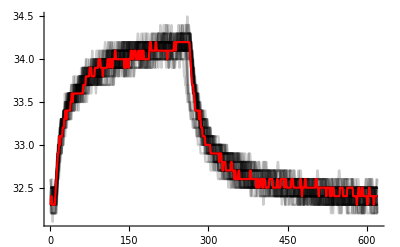

```mathematica
Show[gagTemp, ListLinePlot[gagFitDataFittability[[19]],PlotStyle->Red,PlotRange->All],PlotRange->All]
```

```mathematica
gagFitDataFittability=Delete [gagFitDataFittability,{{1},{4},{10},{22},{34}}];
Dimensions[gagFitDataFittability]
```

{35,620}

## Normalize Data so Baseline is at 0, Set Range Variables

```mathematica
Dimensions[gagFitDataFittability]
```

{35,620}

```mathematica
gagFitDataFittability=baselineNormalize[ gagFitDataFittability];
```

```mathematica
Dimensions[gagFitDataFittability]
```

{35,620}

```mathematica
501/(1000/128.) (*figuring out stim duration*)
```

64.128

```mathematica
stimDuration=256;
stimStart=11;
stimEnd=stimStart+stimDuration-4;
fallStart=stimStart+stimDuration-1;
fallEnd=fallStart+200;
trialLength=Length[gagFitDataFittability[[1]]]
```

620

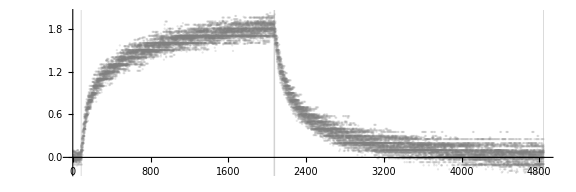

```mathematica
gagTempFitDataFittability=ListPlot[gagFitDataFittability,
GridLines->{{11,11+stimDuration-2,11+stimDuration-2+1,620}*samplingRate,None}, AspectRatio->1/3, ImageSize->72*8,PlotRange->All,PlotStyle->Opacity[0.2,Gray],DataRange->{1,620}*samplingRate]
```

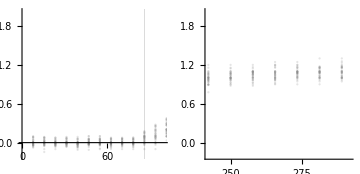

```mathematica
GraphicsRow[
{Show[gagTempFitDataFittability,PlotRange->{{0,100},All},AspectRatio->1],
Show[gagTempFitDataFittability,PlotRange->{stimStart+stimDuration+{-25,+25},All},AspectRatio->1]}, ImageSize->Medium]
```

## Cleaner Plots

```mathematica
Dimensions[Transpose[{gagFitDataFittability,gagColors}]]
```

Transpose::nmtx: The first two levels of {{{0.0777778, 0.0777778, -0.0222222, -0.0222222, -0.0222222, -0.0222222, -0.0222222, -0.0222222, -0.0222222, -0.0222222, 0.0777778, 0.0777778, 0.177778, 0.277778, 0.377778, 0.477778, 0.577778, 0.677778, 0.677778, 0.777778, « 12 », 1.07778, 1.07778, 1.07778, 1.07778, 1.07778, 1.07778, 1.07778, 1.17778, 1.27778, 1.27778, 1.17778, 1.27778, 1.37778, 1.37778, 1.37778, 1.27778, 1.27778, 1.27778, « 570 »}, {« 1 »}, « 32 », {« 1 »}}, « 1 »} cannot be transposed.

{1}

```mathematica
grSDFittability=Show[meanBandPlot[gagFitDataFittability,Gray],
GridLines->{{stimStart,stimEnd+2},None}, PlotRange->{{0,500},All},AspectRatio->1/GoldenRatio,ImageSize->72*7, AxesLabel->{"ms", "K"},Ticks->{Automatic,Automatic}, 
AxesStyle->Thickness[0.0025], BaseStyle->{FontFamily->"Helvetica"},AxesOrigin->{0,0}]
```

Show::gtype: meanBandPlot is not a type of graphics.

Show[1]
 |  |  |  |

```mathematica
gagLegend=Placed[LineLegend[{Directive[gagColors[[4]],Dashed],gagColors[[2]],gagColors[[3]]},{"500ms Raising Phase Fit","2000ms Raising Phase Fit","Falling Phase Fit"},LegendMarkers->None,LabelStyle->8,LegendMarkerSize->{20,10},LegendLabel->Style["Fit Functions",FontWeight->Bold,FontSize->9]],{{1.55,0.6},{2,0.4}}]
```

Placed[,{{1.55,0.6},{2,0.4}}]

```mathematica
grSDGraph=Show[
Show[meanBandPlot[gagFitDataFittability,gagColors[[1]],{-11,620-11}*samplingRate,gagLegend],ImageSize->72*3.5,
GridLines->{{stimStart-12,stimEnd-11+4}*samplingRate,None},GridLinesStyle->Thickness[0.0025],PlotRange->{{-70,620}*samplingRate,{-0.3,2}},AspectRatio->1/GoldenRatio, AxesLabel->{None, None},Ticks->{Table[n,{n,0,4500,1000}],Table[n,{n,0,2,0.5}]},TicksStyle->Directive[Black,9],
AxesStyle->Thickness[0.004], BaseStyle->{FontFamily->"Helvetica"},AxesOrigin->{-10*samplingRate,0},LabelStyle->{FontSize->12,FontWeight->"Bold"},
Prolog->{Opacity[0.15,Gray], Rectangle[{(stimStart-12)*samplingRate,-1},{(stimEnd-11+4)*samplingRate,7}]},
Epilog->{Text["ms",{310*samplingRate,-0.3},BaseStyle->{FontSize->9,FontWeight->"Bold"}],Text["K",{-70*samplingRate,1.1},BaseStyle->{FontSize->9,FontWeight->"Bold"}],Text["140908 Mouse 4",{50*samplingRate,0.05},BaseStyle->{FontSize->2}]}]
]
```

-Graphics-

```mathematica
gagLegend500=Placed[LineLegend[{Directive[gagColors[[4]],Dashed],gagColors[[2]]},{"500ms Raising Phase Fit","2000ms Raising Phase Fit"},LegendMarkers->None,LabelStyle->8,LegendMarkerSize->{20,10},LegendLabel->Style["Fit Functions",FontWeight->Bold,FontSize->9]],{{1.45,0.4},{2,0.4}}]
```

Placed[,{{1.45,0.4},{2,0.4}}]

```mathematica
grSDGraph500=Show[
Show[meanBandPlot[gagFitDataFittability[[;;,1;;75]],gagColors[[1]],{-10,75-11}*samplingRate,gagLegend500],ImageSize->72*3.5,
GridLines->{{stimStart-11,stimEnd-11+4}*samplingRate,None},GridLinesStyle->Thickness[0.0025],PlotRange->{{-12,75}*samplingRate,{-0.2,1.5}},AspectRatio->1/GoldenRatio, AxesLabel->{None, None},Ticks->{Table[n,{n,0,500,100}],Table[n,{n,0,2,0.5}]},TicksStyle->Directive[Black,9],
AxesStyle->Thickness[0.004], BaseStyle->{FontFamily->"Helvetica"},AxesOrigin->{-4*samplingRate,0},LabelStyle->{FontSize->12,FontWeight->"Bold"},
Prolog->{Opacity[0.15,Gray], Rectangle[{0,-1},{(stimEnd-11+4)*samplingRate,7}]},
Epilog->{Text["ms",{36*samplingRate,-0.23},BaseStyle->{FontSize->9,FontWeight->"Bold"}],Text["K",{-12*samplingRate,0.8},BaseStyle->{FontSize->9,FontWeight->"Bold"}],Text["140908 Mouse 4",{7*samplingRate,0.02},BaseStyle->{FontSize->2}]}]
]
```

-Graphics-

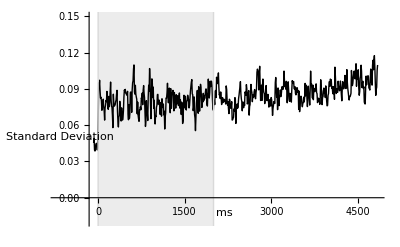

```mathematica
SDGraph= Show[SDPlot[gagFitDataFittability,Black,{-10,trialLength}*samplingRate],PlotRange->{{-90,trialLength}*samplingRate,{-0.02,0.15}},GridLines->{{stimStart-11,stimEnd-11+4}*samplingRate,None},GridLinesStyle->Thickness[0.0025],AxesOrigin->{-20*samplingRate,0},Prolog->{Opacity[0.15,Gray], Rectangle[{0,-1},{(stimEnd-11+4)*samplingRate,7}]},Epilog->{Text["ms",{280*samplingRate,-0.013},BaseStyle->{FontSize->9,FontWeight->"Bold"}],Rotate[Text["Standard Deviation",{-85*samplingRate,0.05},BaseStyle->{FontSize->9,FontWeight->"Bold"}],90 Degree]}]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Dropbox (AG NRO)\Gonzalo\My Stuff\Master thesis\Thermal Imaging\Thermal Imaging Data\140908 Mouse 4(Power correlation)

```mathematica
Export["140908.StdDevoverTime.png",SDGraph,ImageResolution->600]
```

140908.StdDevoverTime.png

```mathematica
Export["140908.StdDevoverTime.pdf",SDGraph,ImageResolution->600]
```

140908.StdDevoverTime.pdf

## Change data to {{time,value}, ....} format and Fit Functions

```mathematica
gagMakeTrialXY[data_, startPoint_Integer, endPoint_Integer]:=Module[{gagTimecourseR},
gagTimecourseR =Range[0, endPoint-startPoint ] *samplingRate;
Flatten[ 
Transpose[{gagTimecourseR,#[[startPoint;;endPoint]]}]&  /@ data,   1
]
];
```

```mathematica
gagModelModelRLog[data_, startPoint_Integer, endPoint_Integer]:=
Module[{tempFunc, tempShift},
Simplify[Evaluate[
NonlinearModelFit[gagMakeTrialXY[data,startPoint, endPoint],  
{0.4*a*Log[0.01*c* x+0.1*b]},
{a,b,c},x]]] 
];
```

```mathematica
gagModelShiftFactorRLog[data_, startPoint_Integer, endPoint_Integer]:=
Module[{tempFunc,tempShift},
tempFunc=gagModelFuncRLog[data, startPoint, endPoint];
tempShift= x /. Flatten[Solve[ Evaluate[tempFunc[x]]==0, x]];
tempShift
];
```

```mathematica
gagModelFuncRLog[data_, startPoint_Integer, endPoint_Integer]:=
Module[{tempFunc},
tempFunc=gagModelModelRLog[data, startPoint, endPoint]["BestFit"];
Evaluate[tempFunc /. x->#]&
];
```

```mathematica
gagModelModelFExp[data_, startPoint_Integer, endPoint_Integer]:=
Module[{},
Simplify[Evaluate[
NonlinearModelFit[gagMakeTrialXY[data,startPoint, endPoint],  
{a*ⅇ^(b*(x+7)) +aa*ⅇ^(b*bb*(x+90)),{0 < a<5,-0.5<b<-0.0001 ,0<aa<5,0<bb<1}},
{a,c,b,aa,bb,cc},x]]]
];
```

```mathematica
gagModelFuncFExp[data_, startPoint_Integer, endPoint_Integer]:=
Module[{tempFunc},
tempFunc=gagModelModelFExp[data, startPoint, endPoint]["BestFit"] ;
Evaluate[tempFunc /. x->#]&
];
```

```mathematica
Manipulate[
Show[grSDFittability,Plot[a*ⅇ^(b*(x)) +aa*ⅇ^(bb*(x)),{x,fallStart,trialLength},PlotRange->All],
PlotRange->All],
{{a,230.},0,1500},{{b,-0.0612},-0.2,0.2},{{aa,0.31},0,5},{{bb,0.0075},-1,0.3}
];
```

## Fit Function

```mathematica
funcR2000=gagModelFuncRLog[gagFitDataFittability,stimStart, stimEnd]
```

0.339309 Log[0.799013+0.117333 #1]&

```mathematica
modelR2000=gagModelModelRLog[gagFitDataFittability,stimStart, stimEnd];
```

```mathematica
shiftR2000=gagModelShiftFactorRLog[gagFitDataFittability,stimStart, stimEnd]
```

1.71297

```mathematica
grRPlot2000=Plot[funcR2000[x+(shiftR2000-1)*samplingRate],{x,0,(stimEnd+2)*samplingRate}, PlotStyle->gagColors[[2]],PlotRange->All];
```

```mathematica
funcR500=gagModelFuncRLog[gagFitDataFittability,stimStart,  stimStart+64]
```

0.398094 Log[0.947556+0.0693583 #1]&

```mathematica
modelR500=gagModelModelRLog[gagFitDataFittability,stimStart, stimStart+64];
```

```mathematica
shiftR500=gagModelShiftFactorRLog[gagFitDataFittability,stimStart,  stimStart+64]
```

0.756136

```mathematica
grRPlot500=Plot[funcR500[x+(*stimStart+*)(shiftR500-1)*samplingRate],{x,2(*((*stimStart+*)shiftR500)*samplingRate*),(stimEnd+2)*samplingRate}, PlotStyle->Directive[Dashed,gagColors[[4]]],PlotRange->All];
```

```mathematica
grRPlot500B=Plot[funcR500[x+(*stimStart+*)(shiftR500-1)*samplingRate],{x,2(*((*stimStart+*)shiftR500)*samplingRate*),500}, PlotStyle->Directive[gagColors[[4]]],PlotRange->All];
```

```mathematica
funcF=gagModelFuncFExp[gagFitDataFittability,fallStart, trialLength]
```

0.988667 ⅇ^(-0.00865717 (7+#1))+0.876656 ⅇ^(-0.00128342 (90+#1))&

```mathematica
grFPlot=Plot[funcF[x-(fallStart-stimStart)*samplingRate],{x,(fallStart-stimStart)*samplingRate,trialLength*samplingRate}, PlotStyle->gagColors[[3]],PlotRange->All];
```

```mathematica
grSDFittability=Show[grSDGraph,grRPlot500,grRPlot500B,grRPlot2000,grFPlot]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Dropbox (AG NRO)\Gonzalo\My Stuff\Master thesis\Thermal Imaging\Thermal Imaging Data\140908 Mouse 4(Power correlation)

```mathematica
Export["140908.AverageFittability.png",grSDFittability,ImageResolution->600]
```

140908.AverageFittability.png

```mathematica
Export["140908.AverageFittability.pdf",grSDFittability,ImageResolution->600]
```

140908.AverageFittability.pdf

```mathematica
grSDFittability500=Show[grSDGraph500,grRPlot500,grRPlot500B,grRPlot2000]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Dropbox (AG NRO)\Gonzalo\My Stuff\Master thesis\Thermal Imaging\Thermal Imaging Data\140908 Mouse 4(Power correlation)

```mathematica
Export["140908.AverageFittability500ms.png",grSDFittability500,ImageResolution->600]
```

140908.AverageFittability500ms.png

```mathematica
Export["140908.AverageFittability500ms.pdf",grSDFittability500,ImageResolution->600]
```

140908.AverageFittability500ms.pdf

```mathematica
modelR2000["AIC"]
```

-18707.3

```mathematica
modelR500["AIC"]
```

-4961.19

```mathematica
modelR2000["RSquared"]
```

0.997056

```mathematica
modelR500["RSquared"]
```

0.994663

```mathematica
funcR500
```

0.398094 Log[0.947556+0.0693583 #1]&

```mathematica
tempData500=gagMakeTrialXY[gagFitDataFittability,stimStart,  stimStart+64];
```

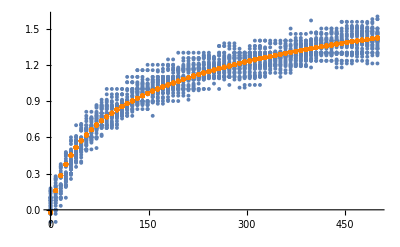

```mathematica
Show[
ListPlot[tempData500],
ListPlot[{#, funcR500[#]}&/@tempData500[[All, 1]], PlotStyle->Orange]
]
```

```mathematica
tempYBar500=Mean[tempData500[[All, 2]]]
```

1.05791

```mathematica
tempSSTotal500=Plus@@(        (#-tempYBar500)^2& /@tempData500[[All, 2]]           )
```

263.116

```mathematica
tempSSRes500=Plus@@(             (#[[2]]-funcR500[#[[1]]])^2& /@tempData500           )
```

14.9932

```mathematica
tempSSReg500=Plus@@(             (funcR500[#[[1]]]-tempYBar500)^2& /@tempData500           )
```

248.123

```mathematica
tempSSRes500+tempSSReg500
```

263.116

```mathematica
tempP500=3;tempN500=65(*Length[tempData500]*)
```

65

```mathematica
tempR2500=1-tempSSRes500/tempSSTotal500
```

0.943017

```mathematica
Correlation[funcR500[#]&/@tempData500[[All, 1]],tempData500[[All, 2]]]^2
```

0.943017

```mathematica
tempR2Adj500=1-(tempSSRes500/(tempN500-tempP500-1))/(tempSSTotal500/(tempN500-1))
```

0.940214

```mathematica
modelR500["RSquared"]
```

0.994663

```mathematica
modelR500["AdjustedRSquared"]
```

0.994656

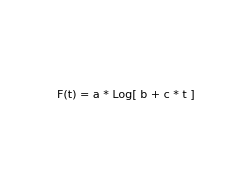

```mathematica
gagraiseFormula=Graphics[Text["F(t) = a * Log[ b + c * t ]",BaseStyle->{FontSize->14,FontWeight->"Bold",FontFamily->"Helvetica"}],ImageSize->72*3.5]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Dropbox (AG NRO)\Gonzalo\My Stuff\Master thesis\Thermal Imaging\Thermal Imaging Data\140908 Mouse 4(Power correlation)

```mathematica
Export["140908.RiseFormula.png",gagraiseFormula,ImageResolution->600]
```

140908.RiseFormula.png

```mathematica
Export["140908.RiseFormula.pdf",gagraiseFormula,ImageResolution->600]
```

140908.RiseFormula.pdf

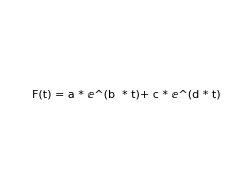

```mathematica
gagfallFormula=Graphics[Text["F(t) = a * ⅇ^(b  * t)+ c * ⅇ^(d * t)",BaseStyle->{FontSize->14,FontWeight->"Bold",FontFamily->"Helvetica"}],ImageSize->72*3.5]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Dropbox (AG NRO)\Gonzalo\My Stuff\Master thesis\Thermal Imaging\Thermal Imaging Data\140908 Mouse 4(Power correlation)

```mathematica
Export["140908.FallFormula.png",gagfallFormula,ImageResolution->600]
```

140908.FallFormula.png

```mathematica
Export["140908.FallFormula.pdf",gagfallFormula,ImageResolution->600]
```

140908.FallFormula.pdf

```mathematica
modelFalling=gagModelModelFExp[gagFitDataFittability,fallStart, trialLength]
```

FittedModel[0.988667 ⅇ^(-0.00865717 (7+x))+0.876656 ⅇ^(-0.00128342 (90+x))]

```mathematica
modelFalling["RSquared"]
```

0.954028